Last modified on: Friday, July 13, 2018 at 15:36

Author Info

Euan Ong

Dariia Porechna

End of Camp Presentation Content

A Machine Learning Analysis of Halting in the SKI Combinator Calculus

Can we learn what we cannot compute?
- The halting problem is the canonical undecidable problem.
- The SKI combinator calculus (SK combinators) can be seen as a reduced form of the untyped lambda calculus, which is Turing-complete; hence, the SKI combinator calculus forms a universal model of computation. 
... Is it possible to use machine learning to predict whether or not an SK combinator expression will halt?

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-
-Graphics--Graphics-

1. Analysis of the growth and halting times of SKI combinator expressions
2. Investigation of the feasibility of a machine learning approach to predicting whether a given SKI combinator expression is likely to halt:
	Naive Bayes on raw expressions: accuracy 0.76, Recurrent Neural Networks: accuracy ~0.5, Random Forest on rasterised images of the first 5 steps of evaluation of a combinator: accuracy 0.88
Microsite: Provides analysis and information about a given or randomly generated SK combinator - check it out at https://wolfr.am/w4j2NT3f

- Attempt analysis of rasterised image with a neural network
- Try to reverse-engineer the Random Forest classification (i.e. what features is it looking for?)
- Implement a vector representation of syntax trees to allow the structure of SK combinators (nesting combinators) to be accurately extracted by a machine learning model
- Analyse SK combinators with a more theoretical approach - proofs of halting / non-halting for certain expressions, for instance - to uncover deeper patterns within these
- Represent lambda calculus expressions in the SK combinator language and analyse these / apply the same methodology to other combinators.

Additional Code Content

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

#### Code

#### Essay:

```mathematica
SKRules={k[x_][y_]:> x,s[x_][y_][z_]:> x[z][y[z]]}
```

```mathematica
SKNext[expr_]:=expr/.SKRules;
```

Returns the next ‘step’ of evaluation of the expression expr - evaluating all functions in expr according to the rules above without evaluating any ‘new’/transformed functions.

```mathematica
SKEvaluate[expr_,n_]:=NestList[#1/.SKRules&,expr,n];
```

Returns the next n steps of evaluation of the expression expr

```mathematica
SKEvaluateUntilHalt[expr_,n_] := FixedPointList[SKNext,expr,n+1];
```

Returns the steps of evaluation of expr until either it reaches a fixed point or it has been evaluated for n steps, whichever comes first.

```mathematica
Column[SKEvaluateUntilHalt[s[k][a][x],10][[1;;-2]]]
```

The I combinator

```mathematica
Column[SKEvaluateUntilHalt[s[k[s[i]]][k][a][b],10][[1;;-2]]]
```

The reversal expression - s[k][s[i]][k][a][b] takes two terms, a and b, and returns b[a].

```mathematica
SKPossibleExpressions[n_]:=(2^n)*Binomial[2*(n-2),n-1]/n
```

The number of possible combinator expressions with leaf size n

```mathematica
SKArray[expr_,n_]:=Characters/@ToString/@SKEvaluate[expr,n];
SKArray[expr_]:=SKArray[expr,10];
```

Generates a list of the steps in the growth of a combinator, where each expression is itself a list of characters (‘s’, ‘k’, ‘[‘, ‘]’)

```mathematica
SKGrid[exp_,n_]:=ArrayPlot[SKArray[exp,n],{ColorRules->{"s"->RGBColor[1,0,0],"k"->RGBColor[0,1,0],"["->RGBColor[0,0,1],"]"->RGBColor[0,0,0]},PixelConstrained->True,Frame->False,ImageSize->1000}];
SKGrid[exp_]:=SKGrid[exp,10];
```

Generates an ArrayPlot of a list given by SKArray, representing the growth of a combinator in a similar manner to that of cellular automata up to step n. The y axis represents time - each row is the next expression in the evaluation of an SK combinator. Red squares indicate ‘S’, blue squares indicate ‘K’, green squares indicate ‘[‘ and black squares indicate ‘]’.

```mathematica
SKRasterize[func_,n_]:=Image[SKGrid[func,n][[1]]];
SKRasterize[func_]:=SKRasterize[func,10];
```

Generates a rasterized version of the ArrayPlot.

```mathematica
SKRasterize[s[s[s]][s][s][s][k],15]
```

The longest running halting expression with leaf size 7, halting in 12 steps (NKS http://www.wolframscience.com/nks/notes-11-12--combinator-properties/)

```mathematica
SKLengths[exp_,n_]:=StringLength/@ToString/@SKEvaluate[exp,n];
```

Returns a list of the lengths of successive expressions until step n

```mathematica
SKPlot[expr_,limit_]:=ListLinePlot[SKLengths[expr,limit],AxesOrigin->{1,0},AxesLabel->{"Number of steps","Length of expression"}];
```

```mathematica
SKPlot[s[s[s]][s][s][s][k],15]
```

A graph of the above combinator (s[s[s]][s][s][s][k])

```mathematica
RecursiveRandomSKExpr[0,current_]:=current;
RecursiveRandomSKExpr[depth_,current_]:= 
RecursiveRandomSKExpr[depth-1,
RandomChoice[{
RandomChoice[{s,k}][current],
current[RecursiveRandomSKExpr[depth-1,RandomChoice[{s,k}]]]
}]
];
RecursiveRandomSKExpr[depth_Integer]:=RecursiveRandomSKExpr[depth,RandomChoice[{s,k}]];
```

A recursive method, repeatedly appending either a combinator to the ' head' of the expression or a randomly generated combinator expression to the ' tail' of the expression. (Hennigan)

```mathematica
replaceWithList[expr_,pattern_,replaceWith_]:=ReplacePart[expr,Thread[Position[expr,pattern]->replaceWith]];
treeToFunctions[tree_]:=ReplaceRepeated[tree,{x_,y_}:>x[y]];
randomTree[leafCount_]:=Nest[ReplacePart[#,RandomChoice[Position[#,x]]->{x,x}]&,{x,x},leafCount-2];
RandomSKExpr[leafCount_]:=treeToFunctions[replaceWithList[randomTree[leafCount],x,RandomChoice[{s,k},leafCount]]];
```

Random combinator generation based on generation of binary trees - each combinator can be expressed as a binary tree with leaves ‘S’ or ‘K’. (http://community.wolfram.com/groups/-/m/t/965400)

```mathematica
exprs = Table[RandomSKExpr[6],10];
ImageCollage[Table[ListLinePlot[SKLengths[exprs[[n]],40]],{n,10}],Background->White]
```

10 randomly generated combinators of size 6, with their lengths plotted until n=40.

```mathematica
exprs = Table[RandomSKExpr[10],10];
ImageCollage[Table[ListLinePlot[SKLengths[exprs[[n]],40]],{n,10}],Background->White]
```

10 randomly generated combinators of size 10, with their lengths plotted until n=20.

```mathematica
exprs = Table[RandomSKExpr[30],10];
ImageCollage[Table[ListLinePlot[SKLengths[exprs[[n]],40]],{n,10}],Background->White]
```

10 randomly generated combinators of size 30, with their lengths plotted until n=40.

```mathematica
CloudEvaluate[exprs = Table[RandomSKExpr[50],10];
ImageCollage[Table[ListLinePlot[SKLengths[exprs[[n]],40]],{n,10}],Background->White]]
```

10 randomly generated combinators of size 50, with their lengths plotted until n=40.

```mathematica
SKHaltLength[expr_,n_]:=Module[{x},
x=Length[SKEvaluateUntilHalt[expr,n+1]];
If[x>n,False,x]
]
```

Returns the number of steps it takes the combinator expr to halt; if expr does not halt within n steps, returns False.

```mathematica
GenerateHaltByTable[depth_,iterations_,number_]:=Module[{exprs,lengths},
exprs = Monitor[Table[RandomSKExpr[depth],{n,number}],n];
lengths = Monitor[Table[SKHaltLength[exprs[[n]],iterations],{n,number}],n];
Return[lengths]
]
```

Generates a table of the halt lengths of number random combinator expressions (False if they do not halt within iterations steps) with leaf size depth.

```mathematica
GenerateHaltData[depth_,iterations_,number_]:=Module[{haltbytable,vals},
haltbytable = GenerateHaltByTable[depth,iterations,number];
vals = BinCounts[Sort[haltbytable],{1,iterations+1,1}];
Table[Total[vals[[1;;n]]],{n,1,Length[vals]}]
]
```

Generates a table of the number of number random combinator expressions (False if they do not halt within iterations steps) with leaf size depth that have halted after a given number of steps

```mathematica
GenerateHaltGraph[depth_,iterations_,number_]:=Module[{cumulative,f},
cumulative=GenerateHaltData[depth,iterations,number];
f=Interpolation[cumulative];
{ListLinePlot[cumulative,PlotRange->{Automatic,{0,number}},GridLines->{{},{number}},Epilog-> {Red,Dashed,Line[{{0,cumulative[[-1]]},{number,cumulative[[-1]]}}]},AxesOrigin->{1,0},AxesLabel->{"Number of steps","Number of combinators halted"}],cumulative[[-1]]}
]
```

Plots a graph of the above data.

```mathematica
CloudEvaluate[GenerateHaltGraph[10,30,1000]]
```

Leaf size 10 : almost all combinators in the sample (997) have halted (99.7 %).

```mathematica
CloudEvaluate[GenerateHaltGraph[20,30,1000]]
```

Leaf size 20: 979 combinators in the sample have halted (97.9%).

```mathematica
CloudEvaluate[GenerateHaltGraph[30,30,1000]]
```

Leaf size 30 : 962 combinators in the sample have halted (96.2 %).

```mathematica
CloudEvaluate[GenerateHaltGraph[40,30,1000]]
```

Leaf size 40 : 944 combinators in the sample have halted (94.4 %).

```mathematica
CloudEvaluate[GenerateHaltGraph[50,30,1000]]
```

Leaf size 50: 889 combinators in the sample have halted (88.9%).

```mathematica
CloudEvaluate[ListLinePlot[Table[{n,GenerateHaltGraph[n,30,1000][[2]]},{n,5,50,1}]]]
```

A graph to show the number of combinators which halt within 30 steps in each of 45 random samples of 1000 combinators, with leaf size varying from 5 to 50.

```mathematica
FitData[data_,func_]:=Module[{fitd},fitd={Fit[data[[1,2,3,4,1]],func,x]};{fitd,Show[ListPlot[data[[1,2,3,4,1]],PlotStyle->Red],Plot[fitd,{x,5,50}]]}]
```

A curve-fitting function: plots the curve of best fit for data with some combination of functions func.

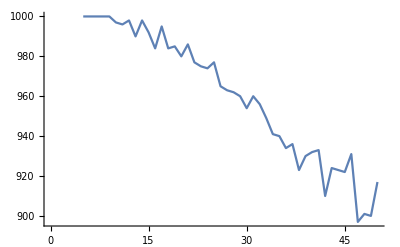
```mathematica
FitData[-Graphics-,{1,x,x^2}]
```

Curve-fitting on the data with a quadratic function yields a reasonably accurate curve of best fit.

```mathematica
SKHaltLength[expr_,n_]:=Module[{x},
x=Length[SKEvaluateUntilHalt[expr,n+1]];
If[x>n,False,x]
]
```

Returns the number of steps expr takes to halt if the given expression expr halts within the limit given (limit), otherwise returns False

```mathematica
GenerateTable[depth_,iterations_,number_]:=Module[{exprs,lengths},
exprs = Monitor[Table[RandomSKExpr[depth],{n,number}],n];
lengths = Monitor[Table[exprs[[n]]-> SKHaltLength[exprs[[n]],iterations],{n,number}],n];
lengths = DeleteDuplicates[lengths];
Return[lengths]
]
```

Returns a list of number expressions with leaf size depth whose elements are associations with key expression and value number of steps taken to halt if the expression halts within iterations steps, otherwise False.

```mathematica
CreateTrainingData[var_]:=Module[{NoHalt,Halt,HaltTrain,Train},
NoHalt = Select[var,#[[2]]==False&];
Halt = Select[var,#[[2]]==True&];
HaltTrain = RandomSample[Halt,Length[NoHalt]];
Train = Join[HaltTrain,NoHalt];
Return[Train]
];
ConvertSKTableToString[sktable_]:=Table[ToString[sktable[[n,1]]]-> sktable[[n,2]],{n,1,Length[sktable]}];
```

```mathematica
CreateRasterizedTrainingData[var_]:=Module[{NoHalt,Halt,HaltTrain,HaltTrainRaster,NoHaltTrainRaster,RasterTrain},
NoHalt = Select[var,#[[2]]==False&];
Halt = Select[var,#[[2]]==True&];
HaltTrain = RandomSample[Halt,Length[NoHalt]];
HaltTrainRaster=Monitor[Table[SKRasterize[HaltTrain[[x,1]],5]-> HaltTrain[[x,2]],{x,1,Length[HaltTrain]}],x];
NoHaltTrainRaster=Monitor[Table[SKRasterize[NoHalt[[x,1]],5]-> NoHalt[[x,2]],{x,1,Length[NoHalt]}],x];
RasterTrain = Join[HaltTrainRaster,NoHaltTrainRaster];
Return[RasterTrain]
];
```

```mathematica
lengths = Flatten[Table[GenerateTable[n,40,2000],{n,5,50,5}]]
```

```mathematica
lengths = lengths/.(a_->b_)/;!(b===False):> (a->True);
```

```mathematica
TrainingData = CreateTrainingData[lengths];
TrainingData2 = ConvertSKTableToString[TrainingData];
```

```mathematica
HaltClassifier1 = Classify[TrainingData2,Method->"Markov"]
```

```mathematica
testlengths = Flatten[Table[GenerateTable[n,40,2000],{n,5,50,5}]]
testlengths = testlengths/.(a_->b_)/;!(b===False):> (a->True);
TestData = CreateTrainingData[testlengths];
TestData2 = ConvertSKTableToString[TestData];
```

```mathematica
TestClassifier1 = ClassifierMeasurements[HaltClassifier1,TestData2]
```

```mathematica
TestClassifier1["Accuracy"]
```

```mathematica
ClassifierInformation[HaltClassifier1]
```

```mathematica
TestClassifier1["ConfusionMatrixPlot"]
```

```mathematica
SKRasterize[RandomSKExpr[50],5]
```

```mathematica
rasterizedlengths = Flatten[Table[GenerateTable[n,40,2000],{n,5,50,5}]];
```

```mathematica
RasterizedTrainingData = CreateRasterizedTrainingData[rasterizedlengths];
```

```mathematica
RasterizeClassifier=Classify[RasterizedTrainingData,Method->"RandomForest"]
```

```mathematica
testrasterizedlengths = Flatten[Table[GenerateTable[n,40,2000],{n,5,50,5}]];
testrasterizedlengths = testrasterizedlengths/.(a_->b_)/;!(b===False):> (a->True);
TestRasterizedData = CreateRasterizedTrainingData[testrasterizedlengths];
```

```mathematica
TestRasterizeClassifier=ClassifierMeasurements[RasterizeClassifier,TestRasterizedData]
```

```mathematica
TestRasterizeClassifier["Accuracy"]
```

```mathematica
ClassifierInformation[RasterizeClassifier]
```

```mathematica
TestRasterizeClassifier["ConfusionMatrixPlot"]
```

#### Microsite (some functions have the same name as in the essay but do different things)

SK_Functions:

```mathematica
(*RandomSKExpr[0,current_]:=current;
RandomSKExpr[depth_,current_]:= 
RandomSKExpr[depth-1,
RandomChoice[{
RandomChoice[{s,k}][current],
current[RandomSKExpr[depth-1,RandomChoice[{s,k}]]]
}]
];
RandomSKExpr[depth_Integer]:=RandomSKExpr[depth,RandomChoice[{s,k}]];
RandomSK[depth_Integer]:=First[RandomSKExpr[depth]];*)

(*from http://community.wolfram.com/groups/-/m/t/965400 *)
replaceWithList[expr_,pattern_,replaceWith_]:=ReplacePart[expr,Thread[Position[expr,pattern]->replaceWith]];
treeToFunctions[tree_]:=ReplaceRepeated[tree,{x_,y_}:>x[y]];
randomTree[leafCount_]:=Nest[ReplacePart[#,RandomChoice[Position[#,x]]->{x,x}]&,{x,x},leafCount-2];

combChar = LetterCharacter | DigitCharacter | Verbatim["*"] | "$";

validStringSymbolsQ[s_] :=
	StringMatchQ[s, (combChar | "[" | "]" | "(" | ")" | WhitespaceCharacter)..]

validCombinatorStringQ[s_] := 
	If[SyntaxQ[StringReplace[s, x:(combChar).. :> "\"" <> x <> "\""]] && 
		StringMatchQ[s, 
			(combChar | "[" | "]" | WhitespaceCharacter)..] && 
		StringCount[s, "[" ~~ (""|Whitespace) ~~ "["] == 0 && 
		StringCount[s, ("]") ~~ (""|Whitespace) ~~ combChar] == 0 && 
		StringCount[s, "[" ~~ ("" | Whitespace) ~~ "]"] == 0, True, False]
(*/from*)

RandomSKExpr[leafCount_]:=treeToFunctions[replaceWithList[randomTree[leafCount],x,RandomChoice[{s,k},leafCount]]];

ValidSKCombinatorQ[s_]:=If[(!Length[Cases[Characters[s],Except[PatternSequence["s"|"k"|"["|"]"]]]]>0)&&validCombinatorStringQ[s]===True,True,False];

makeFailure[message_,context_:<||>]:=Failure[
"RestrictionFailure",<|
"MessageTemplate"->message,
"MessageParameters"->context
|>]

SKCombinatorValidator[expression_]:=With[{expr=Interpreter["String"][expression]},
If[ValidSKCombinatorQ[expr],expr,makeFailure["SK combinator expression invalid."]]
]

SKRules={k[x_][y_]:> x,s[x_][y_][z_]:> x[z][y[z]]};
SKNext[expr_]:=expr/.SKRules;
SKEvaluate[expr_,n_]:=NestList[#1/.SKRules&,expr,n];
SKEvaluate[expr_]:=SKEvaluate[expr,10];
SKArray[expr_]:=SKArray[expr,10];
SKArray[expr_,n_]:=Characters/@ToString/@SKEvaluate[expr,n];
SKGrid[exp_]:=SKGrid[exp,10];
SKGrid[exp_,n_]:=ArrayPlot[SKArray[exp,n],{ColorRules->{"s"->RGBColor[1,0,0],"k"->RGBColor[0,1,0],"["->RGBColor[0,0,1],"]"->RGBColor[0,0,0]},PixelConstrained->True,Frame->False,ImageSize->1000}];
SKRasterize[func_]:=SKRasterize[func,10];
SKRasterize[func_,n_]:=Image[SKGrid[func,n][[1]]];

SKLeafCount[expr_]:=LetterCounts[ToString@expr][["s"]]+LetterCounts[ToString@expr][["k"]];

SKLengths[exp_,n_]:=StringLength/@ToString/@SKEvaluate[exp,n]; (*gives length of each step of expression exp until limit n*)

SKEvaluateUntilHalt[expr_,n_] := FixedPointList[SKNext,expr,n+1]; (*returns list of steps of evaluation of expression until n+1th step*)

SKHaltLength[expr_,n_]:=Module[{x},
x=Length[SKEvaluateUntilHalt[expr,n+1]];
If[x>n,False,x]
] 
(*returns false if doesn't halt; otherwise returns length*)

(*redundant*)
HaltIf[n_,list_]:=SameQ[list[[n]],list[[n-1]]] (*does this halt at n?*)
HaltBy[n_,lens_]:=Count[lens,x_/;HaltIf[n,x]==True] (*how many in lens halt by n?*)
SKHalt[expr_,limit_]:=Module[{evaluate},
evaluate = SKEvaluate[expr,limit];
HaltIf[limit,evaluate]
] 
(*redundant*)

SKPlot[expr_,limit_]:=ListLinePlot[SKLengths[expr,limit]]
(*Plots a graph of the lengths of each step of a combinator - a good way to see if it might halt*)

(*TestClassifier[c_]:=Module[{x,y,z},
x=RandomSKExpr[10];
y = c[ToString[x]];
z = SKPlot[x,50];
Return[{y,z,MemberQ[TrainingData2,x]}]
]*)

GenerateTable[depth_,iterations_,number_]:=Module[{exprs,lengths},
exprs = Monitor[Table[RandomSKExpr[depth],{n,number}],n];
lengths = Monitor[Table[exprs[[n]]-> SKHalt[exprs[[n]],iterations],{n,number}],n];
lengths = DeleteDuplicates[lengths];
Return[lengths]
]
GenerateHaltByTable[depth_,iterations_,number_]:=Module[{exprs,lengths},
exprs = Monitor[Table[RandomSKExpr[depth],{n,number}],n];
lengths = Monitor[Table[SKHaltLength[exprs[[n]],iterations],{n,number}],n];
Return[lengths]
]
GenerateHaltData[depth_,iterations_,number_]:=Module[{haltbytable,vals},
haltbytable = GenerateHaltByTable[depth,iterations,number];
vals = BinCounts[Sort[haltbytable],{1,iterations+1,1}];
Table[Total[vals[[1;;n]]],{n,1,Length[vals]}]
]
GenerateHaltGraph[depth_,iterations_,number_]:=Module[{cumulative},
cumulative=GenerateHaltData[depth,iterations,number];
ListLinePlot[cumulative,PlotRange->{Automatic,{0,number}},GridLines->{{},{number}}]
]
GenerateSiteHaltGraph[depth_,iterations_,number_, point_]:=Module[{cumulative,f},
cumulative=GenerateHaltData[depth,iterations,number];
f=Interpolation[cumulative];
{ListLinePlot[cumulative,PlotRange->{Automatic,{0,number}},GridLines->{{},{number}},Epilog-> {Red,Dashed,Line[{{point,0},{point,f[point]}}],Line[{{0,f[point]},{point,f[point]}}]},AxesOrigin->{1,0},AxesLabel->{"Number of steps","Number of combinators halted"}],f[point]}
]
GenerateSiteHaltGraphHaltCase[depth_,iterations_,number_]:=Module[{cumulative,f},
cumulative=GenerateHaltData[depth,iterations,number];
f=Interpolation[cumulative];
{ListLinePlot[cumulative,PlotRange->{Automatic,{0,number}},GridLines->{{},{number}},Epilog-> {Red,Dashed,Line[{{0,cumulative[[-1]]},{number,cumulative[[-1]]}}]},AxesOrigin->{1,0},AxesLabel->{"Number of steps","Number of combinators halted"}],cumulative[[-1]]}
]
GenerateTableDepthRange[mindepth_,maxdepth_,iterations_,numberateachdepth_]:=Monitor[Flatten[Table[GenerateTable[n,iterations,numberateachdepth],{n,mindepth,maxdepth}]],n]
ConvertSKTableToString[sktable_]:=Table[ToString[sktable[[n,1]]]-> sktable[[n,2]],{n,1,Length[sktable]}];

CreateTrainingData[var_]:=Module[{NoHalt,Halt,HaltTrain,HaltTrainRaster,NoHaltTrainRaster,RasterTrain},
NoHalt = Select[var,#[[2]]==False&];
Halt = Select[var,#[[2]]==True&];
HaltTrain = RandomSample[Halt,Length[NoHalt]];
HaltTrainRaster=Monitor[Table[SKRasterize[HaltTrain[[x,1]],5]-> HaltTrain[[x,2]],{x,1,Length[HaltTrain]}],x];
NoHaltTrainRaster=Monitor[Table[SKRasterize[NoHalt[[x,1]],5]-> NoHalt[[x,2]],{x,1,Length[NoHalt]}],x];
RasterTrain = Join[HaltTrainRaster,NoHaltTrainRaster];
Return[RasterTrain]
];

GetSKHalt[trainingdata_,halt_]:=Select[trainingdata,#[[2]]==halt&];

TestClassifier[classifier_,trainingdata_,haltdepth_,classifierlength_]:=Module[{x,y,z},
x=RandomSKExpr[classifierlength];
y = classifier[ToString[x]];
z = SKPlot[x,haltdepth];
Return[{y,z,MemberQ[trainingdata,x]}] (*does it halt?,graph,is it in data?*)
]
TestClassifierRasterize[classifier_,trainingdata_,haltdepth_,classifierlength_]:=Module[{x,y,z},
x=RandomSKExpr[classifierlength];
y = classifier[SKRasterize[x]];
z = SKPlot[x,haltdepth];
Return[{y,z,MemberQ[trainingdata,SKRasterize[x]]}] (*does it halt?,graph,is it in data?*)
]
TestClassifier[classifier_,trainingdata_]:=TestClassifier[classifier,trainingdata,40,10]
TestClassifierRasterize[classifier_,trainingdata_]:=TestClassifierRasterize[classifier,trainingdata,40,5]
ImportDataset[name_]:=Get["/Users/eohomegrownapps/CODE/Assorted codings/Wolfram/SK-Combinators/"<>name]

ToBase4String[sk_]:=StringReplace[ToString[sk],{"s"->"3","["-> "2","k"->"1","]"-> "0"}]
```

Site:

```mathematica
CloudConnect[]
```

euan.l.y.ong@gmail.com

```mathematica
ProcessHeadingOutput[val_,exp_]:=Column[{Style[val[[1]],25],val[[2]],Delimiter}];
```

```mathematica
ReturnExpression[exp_]:=exp;
```

```mathematica
ColumnSpaced[data_]:=Grid[List/@data,Spacings->2];
```

```mathematica
EvaluateHaltData[exp_]:=Module[{Limit,Evaluated,Halt},
Limit=30;
Evaluated=SKEvaluateUntilHalt[exp,30];
Halt =False; (* a hack *)
If[Length[Evaluated]>Limit,
If[Evaluated[[-1]]===Evaluated[[-2]],
Halt =Limit,
Halt = False],
Halt=Length[Evaluated]-1];
{Evaluated[[1;;-2]],Halt}
]
```

```mathematica
EvaluateExpression[exp_,evaluatedata_]:=Module[{Limit,Halt},
Limit=30;
Halt="Halted in "<>ToString[Length[evaluatedata[[1]]]-1]<>" step(s)";
If[evaluatedata[[2]]===False,Halt="Did not halt within "<>ToString[Limit]<>" steps",Halt="Halted in "<>ToString[Length[evaluatedata[[1]]]-1]<>" step(s)"];
ColumnSpaced[{Halt,Grid[Transpose[{Range[0,Length[evaluatedata[[1]]]-1],evaluatedata[[1]]}],Frame->All]}]
]
```

```mathematica
RasteriseExpression[exp_,evaluatedata_]:=(*Module[{Evaluated,StepsNumber,Halt,Limit,KeyRow,Explain},
Limit=30;
Halt=evaluatedata[[2]];
If[evaluatedata[[2]]==False,Halt=Limit,Halt=evaluatedata[[2]]];
StepsNumber="Initial state and first "<>ToString[Halt-1]<>" step(s) of evaluation:";
Evaluated=Rasterize[ArrayPlot[Characters/@ToString/@evaluatedata[[1]],{ColorRules->{"s"->RGBColor[1,0,0],"k"->RGBColor[0,1,0],"["->RGBColor[0,0,1],"]"->RGBColor[0,0,0]},PixelConstrained->True,Frame->False,ImageSize->1000}]];
KeyRow=Row[{"Key:  ",RGBColor[1,0,0],"  represents 's',  ",RGBColor[0,1,0],"  represents 'k',  ",RGBColor[0,0,1],"  represents '[',  ",RGBColor[0,0,0],"  represents ']'"}];
Explain="The nth row of the image represents the nth step of evaluation of the combinator."; 
Column[{StepsNumber,KeyRow,Explain,Evaluated}]*)
Module[{Evaluated,StepsNumber,KeyLegend,Explain},
StepsNumber="Initial state and first 5 steps of evaluation:";
Evaluated=Rasterize[SKGrid[exp,5]];
(*KeyRow=Row[{"Key:  ",RGBColor[1,0,0],"  represents 's',  ",RGBColor[0,1,0],"  represents 'k',  ",RGBColor[0,0,1],"  represents '[',  ",RGBColor[0,0,0],"  represents ']'"}];*)
KeyLegend=Rasterize[SwatchLegend[{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[0,0,0]},{"s","k","[","]"},LegendLayout->"Row",LegendLabel->"Key:"]];
Explain="The nth row of the image represents the nth step of evaluation of the combinator."; 
ColumnSpaced[{StepsNumber,Explain,KeyLegend,Evaluated}]
]
```

```mathematica
LengthGraph[exp_,evaluatedata_]:=Module[{Description,PlotLengths},
Description="As the combinator is evaluated, its length changes. This graph plots length of combinator against number of steps of evaluation.";
PlotLengths=ListLinePlot[StringLength/@ToString/@evaluatedata[[1]],AxesOrigin->{1,0},AxesLabel->{"Number of steps","Length of expression"}];
ColumnSpaced[{Description,PlotLengths}]
]
```

```mathematica
StatisticalAnalysis[exp_,evaluatedata_]:=Module[{Limit,DataSize,LeafCount,Description,Graph,HaltDescription,DescFinal},
Limit=30;
DataSize = 1000;
LeafCount=SKLeafCount[exp];
Graph = If[evaluatedata[[2]]===False,GenerateSiteHaltGraphHaltCase[LeafCount,Limit,DataSize],GenerateSiteHaltGraph[LeafCount,Limit,DataSize,evaluatedata[[2]]]];
Description="This combinator has "<>ToString[LeafCount]<>" leaves.\nThis combinator falls within the "<>ToString[Floor[Graph[[2]]/DataSize*100]]<>"th percentile of a random sample of "<>ToString[DataSize]<>" combinators with leaf size "<>ToString[LeafCount]<>", halting after "<>ToString[evaluatedata[[2]]]<>" steps - on average, "<>ToString[(Graph[[2]]/DataSize*100)//N]<>"% of combinators from this sample halt before this one.\nA graph demonstrating this follows:";
HaltDescription="This combinator has "<>ToString[LeafCount]<>" leaves.\nThis combinator is above the "<>ToString[Floor[Graph[[2]]/DataSize*100]]<>"th percentile of a random sample of "<>ToString[DataSize]<>" combinators with leaf size "<>ToString[LeafCount]<>", not having halted after "<>ToString[Limit]<>" steps - on average, at least "<>ToString[(Graph[[2]]/DataSize*100)//N]<>"% of combinators from this sample halt before this one.\nA graph demonstrating this follows:";
DescFinal=If[evaluatedata[[2]]===False,HaltDescription,Description];
ColumnSpaced[{DescFinal,Graph[[1]]}]
] (*use Daria's statistics*)
```

```mathematica
SKMachineLearn[exp_,evaluatedata_]:=Module[{Limit,Description,MLRaster,Probability,NoHaltStatement,HaltStatement,Analysis},
Limit=30;
Description="A machine learning model (using logistic regression) has been trained on a sample of 1456 rasterised images of the first 5 steps of random SK combinator expressions with leaf length 50, achieving 91.0% accuracy when classifying a test set of 1456 random SK combinator expressions as halting or non halting (before 40 steps).";
MLRaster = SKRasterize[exp,5];
Probability=RasterizeClassifier[MLRaster,"Probabilities"];
NoHaltStatement="does not halt within "<>ToString[Limit]<>" steps";
HaltStatement="halts after "<>ToString[evaluatedata[[2]]]<>" step(s)";
Analysis = "This particular expression, which "<>If[evaluatedata[[2]]===False,NoHaltStatement,HaltStatement]<>", is classified as having a "<>ToString[NumberForm[Probability[True]*100,3]]<>"% probability of halting, and a "<>ToString[NumberForm[Probability[False]*100,3]]<>"% probability of not halting (before 40 steps).";
ColumnSpaced[{Description,Analysis}]
]
```

```mathematica
ClearAll[SKAnalytics];
SKAnalytics[exp_]:=Module[{Headings,Evaluated,expreval},
ClearAll[s];
ClearAll[k];
expreval = ToExpression[exp];
Evaluated = EvaluateHaltData[expreval];
Headings={{"Expression:",ReturnExpression[exp]},{"Visualisation:",RasteriseExpression[expreval,Evaluated]},{"Graph of Evaluated Expression Lengths:",LengthGraph[expreval,Evaluated]},{"Statistical Analysis of Halting Time:",StatisticalAnalysis[expreval,Evaluated]},{"Machine Learning Analysis of Halting:",SKMachineLearn[expreval,Evaluated]},{"Evaluated expression:",EvaluateExpression[expreval,Evaluated]}};
ColumnSpaced[ProcessHeadingOutput[#,exp]&/@Headings]
]
```

```mathematica
CloudDeploy[FormPage[
{"Expression"-><|"Interpreter"->SKCombinatorValidator, "Help" -> "Input a valid SK combinator expression or use the random expression above.","Input":> ToString@RandomSKExpr[50]|>},
SKAnalytics[#Expression]&,
AppearanceRules-><|"Title"->"SK Combinator Expression Analysis"|>,
PageTheme->"Red"
],
"SKCombinators",
Permissions->"Public"
]
```

CloudObject[https://www.wolframcloud.com/objects/euan.l.y.ong/SKCombinators]

#### Additional Text Content

Microsite (analysing combinators) available at https://www.wolframcloud.com/objects/euan.l.y.ong/SKCombinators

#### Conclusions in Detail

### Conclusions

The results of this exploration were somewhat surprising, in that a machine learning approach to determining whether or not a program will terminate appears to some extent viable - out of all the methods attempted, the random forest classifier applied to a rasterised image of the first five steps of the evaluation of a combinator achieved the highest accuracy of 0.88 on a test dataset of 1454 random SK combinator expressions. Note, though, that what is actually being determined here is whether or not a combinator will halt before some n steps (here, n=40) - we are classifying between combinators that ‘definitely halt’ and combinators which are ‘possibly non-halting’.

### Microsite

As an extension to this project, a Wolfram microsite was created and is accessible at https://www.wolframcloud.com/objects/euan.l.y.ong/SKCombinators - within this microsite, a user can view a rasterised image of a combinator, a graph of the length of the combinator as it is evaluated, a statistical analysis of halting time relative to other combinators with the same leaf size and a machine learning prediction of whether or not the combinator will halt within 40 steps.

A screenshot of the microsite evaluating a random SK combinator expression

### Implications, Limitations and Further Work

Although the halting problem is undecidable, the field of termination analysis - attempting to determine whether or not a given program will eventually terminate - has a variety of applications, for instance in program verification. Machine learning approaches to this problem would not only help explore this field in new ways but could also be implemented in, for instance, software debuggers.

The principal limitations of this method are that we are only predicting whether or not a combinator will halt in a finite number k of steps - while this could be a sensible idea if k is large, at present this system is very impractical due to small datasets and a small value of k used to train the classifier (k = 40). Another issue with the machine learning technique used is that the visualisations have different dimensions (longer combinators will generate longer images), and when the images are preprocessed and resized before being fed into the random forest model, downsampling/upsampling can lead to loss of data decreasing the accuracy of the model.

From a machine learning perspective, attempts at analysis of the rasterised images with a neural network could well prove fruitful, as would an implementation of a vector representation of syntax trees to allow the structure of SK combinators (nesting combinators) to be accurately extracted by a machine learning model.

Future theoretical research could include a deeper exploration of Lathrop’s probabilistic method of determining k, an investigation of the ‘halting’ features the machine learning model is looking for within the rasterised images, a more general analysis of SK combinators (proofs of halting / non-halting for certain expressions, for instance) to uncover deeper patterns, or even an extension of the analysis carried out in the microsite to lambda calculus expressions (which can be transformed to an ‘equivalent’ SK combinator expression).

#### All Visualizations

```mathematica
SKRasterize[s[s[s]][s][s][s][k],15]
```

The longest running halting expression with leaf size 7, halting in 12 steps (NKS http://www.wolframscience.com/nks/notes-11-12--combinator-properties/)

```mathematica
SKPlot[s[s[s]][s][s][s][k],15]
```

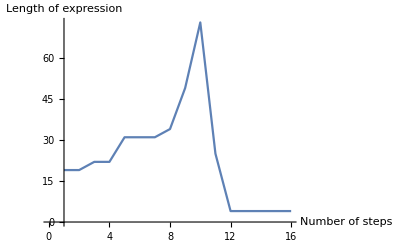

A graph of the above combinator

```mathematica
exprs = Table[RandomSKExpr[6],10];
ImageCollage[Table[ListLinePlot[SKLengths[exprs[[n]],40]],{n,10}],Background->White]
```

10 randomly generated combinators of size 6, with their lengths plotted until n=40.

```mathematica
exprs = Table[RandomSKExpr[10],10];
ImageCollage[Table[ListLinePlot[SKLengths[exprs[[n]],40]],{n,10}],Background->White]
```

-Graphics-

10 randomly generated combinators of size 10, with their lengths plotted until n = 20.

```mathematica
exprs = Table[RandomSKExpr[30],10];
ImageCollage[Table[ListLinePlot[SKLengths[exprs[[n]],40]],{n,10}],Background->White]
```

-Graphics-

10 randomly generated combinators of size 30, with their lengths plotted until n=40.

CloudEvaluate[exprs = Table[RandomSKExpr[50],10];
ImageCollage[Table[ListLinePlot[SKLengths[exprs[[n]],40]],{n,10}],Background→White]]
-Graphics-

10 randomly generated combinators of size 50, with their lengths plotted until n = 40.

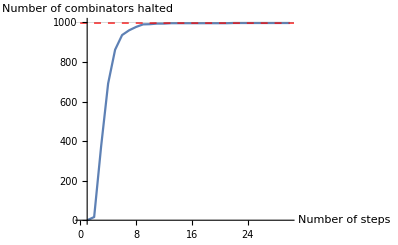
{-Graphics-,997}

```mathematica
CloudEvaluate[GenerateHaltGraph[10,30,1000]]
```

Leaf size 10: almost all combinators in the sample (997) have halted (99.7%).

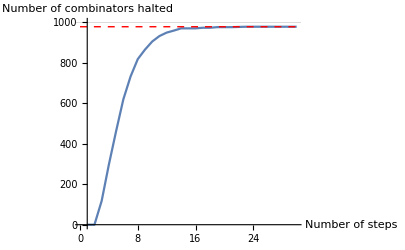
{-Graphics-,979}

```mathematica
CloudEvaluate[GenerateHaltGraph[20,30,1000]]
```

Leaf size 20: 979 combinators in the sample have halted (97.9%).

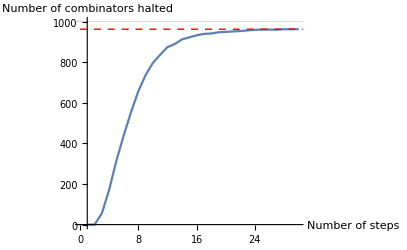
{-Graphics-,962}

```mathematica
CloudEvaluate[GenerateHaltGraph[30,30,1000]]
```

Leaf size 30: 962 combinators in the sample have halted (96.2%).

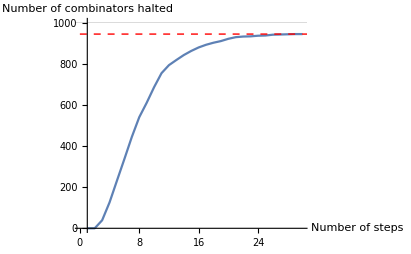
{-Graphics-,944}

```mathematica
CloudEvaluate[GenerateHaltGraph[40,30,1000]]
```

Leaf size 40: 944 combinators in the sample have halted (94.4%).

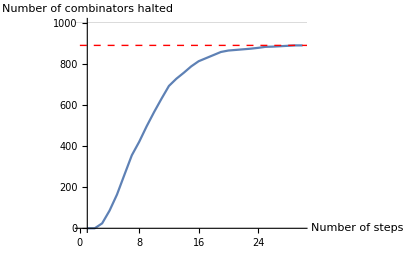
{-Graphics-,889}

```mathematica
CloudEvaluate[GenerateHaltGraph[50,30,1000]]
```

Leaf size 50: 889 combinators in the sample have halted (88.9%).

```mathematica
CloudEvaluate[ListLinePlot[Table[{n,GenerateHaltGraph[n,30,1000][[2]]},{n,5,50,1}]]]
```

A graph to show the number of combinators which halt within 30 steps in each of 45 random samples of 1000 combinators, with leaf size varying from 5 to 50.

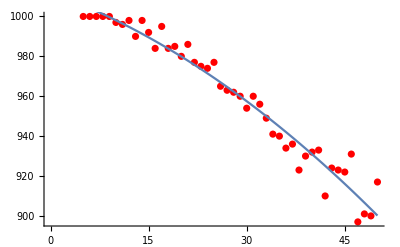
{{1012.07-1.18915 x-0.0209805 x^2},-Graphics-}

```mathematica
FitData[-Graphics-,{1,x,x^2}]
```

Curve-fitting on the data with a quadratic function yields a reasonably accurate curve of best fit.

Markov Classifier information

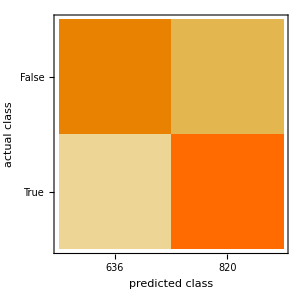

```mathematica
TestClassifier1["ConfusionMatrixPlot"]
```

```mathematica
SKRasterize[RandomSKExpr[50],5]
```

Random Forest classifier information

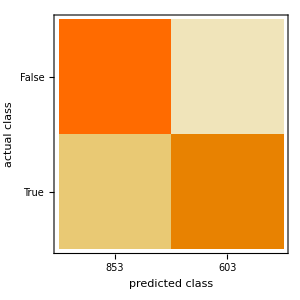

```mathematica
TestRasterizeClassifier["ConfusionMatrixPlot"]
```

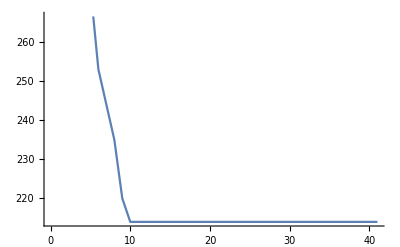

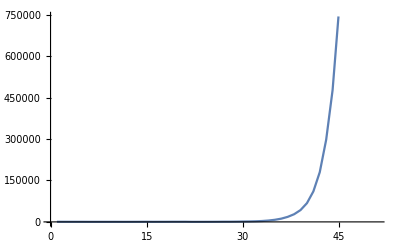

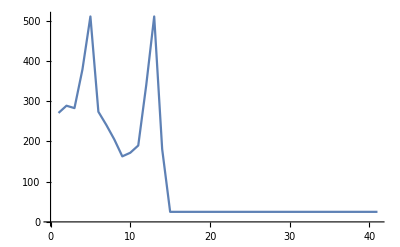

Table of machine learning metrics for the two models

Microsite analysis

#### Data Sources Links/References

All data sources were generated using code featured in this notebook.

#### Background Info Links/References

#### Background Info Links

http://wiki.c2.com/?EssAndKayCombinators
https://en.wikipedia.org/wiki/Combinatory_logic
https://en.wikipedia.org/wiki/SKI_combinator_calculus
https://brilliant.org/wiki/halting-problem/

#### References

A. Church and J. B. Rosser: Some properties of conversion. Transactions of the American Mathematical Society, 39 (3): 472–482, 2018

R. H. Lathrop: On the learnability of the uncomputable. ICML 1996: 302-309.

C. S. Calude and M. Dumitrescu: A probabilistic anytime algorithm for the halting problem. Computability 7(2-3): 259-271, 2018.

L. G. Valiant: A theory of the learnable. Communications of the Association for Computing Machinery 27, (11): 1134-1142, 1984.

S. Wolfram: A New Kind of Science. 1121-1122, 2002.

E. Parfitt: Ways that combinators evaluate from the Wolfram Community—A Wolfram Web Resource. (2017)
http://community.wolfram.com/groups/-/m/t/965400

S-C Mu: Agda.Termination.Termination http://www.iis.sinica.edu.tw/~scm/Agda/Agda-Termination-Termination.html

#### Keywords

Provide keywords as items

Machine Learning

Halting Problem

SKI Combinator Calculus

Wolfram Science

Computer Science

Data Science

#### Other information

Computational essay can be downloaded at